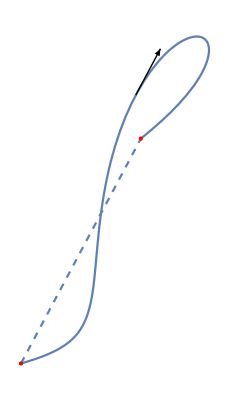

```mathematica
x[t_]:=(t-1)*(1-t/π)+Cos[t] (t/π)
y[t_]:=(t-1)*(1-t/π)+Sin[t] (t/π)

Show[ParametricPlot[{x[t],y[t]},{t,0,2 π},Axes->False],Plot[((y[2 π]-y[0])/(x[2 π]-x[0])) t+(y[0]-(y[2 π]-y[0])/(x[2 π]-x[0]) x[0]),{t,x[0],x[2 π]},PlotStyle->Dashed],Graphics[{Red,PointSize[Large],Point[{x[0],y[0]}],Point[{x[2 π],y[2 π]}]}],

Graphics[Arrow[{{x[t],y[t]},{x[t]-x'[t]/(√(x'[t]^2+y'[t]^2)),y[t]-y'[t]/(√(x'[t]^2+y'[t]^2))}}/.{t->3.24}],Axes->True,AxesLabel->{"x","y"}]
]
```

```mathematica
Manipulate[
{y'[t]/x'[t],(y[2 π]-y[0])/(x[2 π]-x[0])}//N
,{t,0,2π}]
```